# Power effect on temperature rise (141118)

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140908 Mouse 4(Power correlation)

```mathematica
samplingRate=1000./128
```

7.8125

```mathematica
gagFiles=FileNames["*.mat"]
```

{140908-01-200um-5mW,500ms,0'2Hz,40T.mat,140908-02-200um-2,5mW,500ms,0'2Hz,40T.mat,140908-03-200um-5mW,500ms,0'2Hz,40T.mat,140908-04-200um-7,5mW,500ms,0'2Hz,40T.mat,140908-05-200um-10mW,500ms,0'2Hz,40T.mat,140908-06-200um-5mW,500ms,0'2Hz,40T.mat,140908-07-200um-2,5mW,2000ms,0'2Hz,40T.mat,140908-08-200um-20mW,10ms,0'2Hz,40T(pulsed at 25Hz).mat}

## 5 mW 500 ms

## Functions

```mathematica
baselineNormalize[data_]:=Module[{},
(#-Mean[#[[1;;9]]])&/@data
];
```

```mathematica
meanBandPlot[data_, color_]:=Module[{means, sds},
means=Mean/@Transpose[data];
sds=StandardDeviation/@Transpose[data];
ListLinePlot[{means-sds, means+sds},
PlotStyle->None,
PlotRange->All,
Filling->{1->{{2},Opacity[1,color]}}
]
];
```

```mathematica
meanPlot[data_, color_, dataRange_:Automatic]:=
Module[{means,timePoints},
means=Mean/@Transpose[data];
If[dataRange===Automatic,
ListLinePlot[means,PlotStyle->{color,Thick}],
timePoints=Rescale[Range[Length[means]],{1,Length[means]},dataRange];
ListLinePlot[Transpose[{timePoints,means}],
PlotStyle->{color,Thick},PlotRange->All]
]


];
```

```mathematica
means[data_]:=Module[{means, sds},
Mean/@Transpose[data]
];
```

```mathematica
trialPointPlot[data_, color_]:=Module[{},
ListPlot[data,PlotStyle->Opacity[0.2,color]]
];
```

```mathematica
trialPointLogPlot[data_, color_]:=Module[{},
ListLogPlot[data,PlotStyle->Opacity[0.2,color]]
];
```

```mathematica
gagColors= {LightBlue,Blue,Darker[Blue],Purple,Pink,Red,Orange,Yellow,LightGreen,Green, Darker[Green]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
gagColors=Table[ColorData["GrayTones",1-n],{n,0.2,1,0.8/3}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Load Data

```mathematica
gagFitDataPow=Map[Import,gagFiles];
Dimensions/@gagFitDataPow
```

{{1,40,620},{1,40,620},{1,40,620},{1,40,620},{1,40,620},{1,40,620},{1,40,620},{1,38,620}}

```mathematica
gagFitDataPow= gagFitDataPow[[2;;5]];
Dimensions[gagFitDataPow]
```

{4,1,40,620}

```mathematica
gagFitDataPow=Flatten[gagFitDataPow,1];
Dimensions/@gagFitDataPow
```

{{40,620},{40,620},{40,620},{40,620}}

### Remove bad trials if necessary

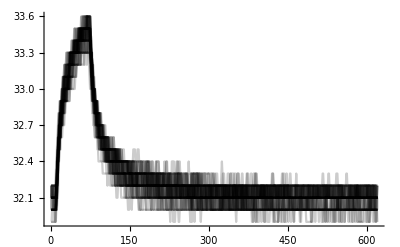
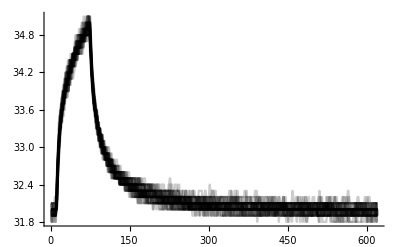
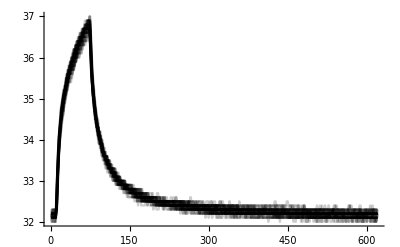
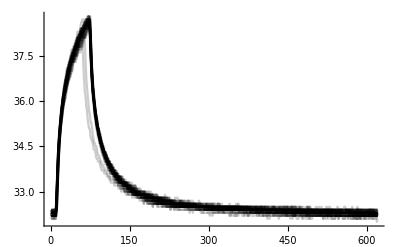

```mathematica
ListLinePlot[#,PlotStyle->Opacity[0.2,Black],PlotRange->All]&/@gagFitDataPow
```

```mathematica
gagTemp=ListLinePlot[gagFitDataPow[[3]],PlotStyle->Opacity[0.2,Black],PlotRange->All]
```

-Graphics-

```mathematica
Ordering[gagFitDataPow[[2]][[;;, 1]],1]
```

{13}

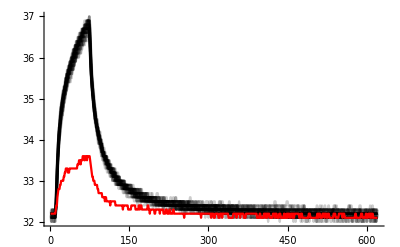

```mathematica
Show[gagTemp, ListLinePlot[gagFitDataPow[[1]][[11]],PlotStyle->Red,PlotRange->All],PlotRange->All]
```

```mathematica
gagFitDataPow[[4]]=Delete [gagFitDataPow[[4]],{{5},{37}}];
Dimensions[gagFitDataPow[[4]]]
```

{38,620}

```mathematica
gagFitDataPow[[1]]=Delete [gagFitDataPow[[1]],{{33},{37}}];
Dimensions[gagFitDataPow[[1]]]
```

{38,620}

```mathematica
gagFitDataPow[[2]]=Delete [gagFitDataPow[[2]],{{7},{37}}];
Dimensions[gagFitDataPow[[2]]]
```

{38,620}

```mathematica
gagFitDataPow[[3]]=Delete [gagFitDataPow[[3]],{{7},{37}}];
Dimensions[gagFitDataPow[[3]]]
```

{38,620}

```mathematica
Dimensions/@gagFitDataPow
```

{{38,620},{38,620},{38,620},{38,620}}

## Normalize Data so Baseline is at 0, Set Range Variables

```mathematica
Dimensions/@gagFitDataPow
```

{{38,620},{38,620},{38,620},{38,620}}

```mathematica
gagFitDataPow=baselineNormalize/@ gagFitDataPow;
```

```mathematica
Dimensions/@gagFitDataPow
```

{{38,620},{38,620},{38,620},{38,620}}

```mathematica
501/(1000/128.) (*figuring out stim duration*)
```

64.128

```mathematica
stimDuration=64;
stimStart=11;
stimEnd=stimStart+stimDuration-4;
fallStart=stimStart+stimDuration-1;
fallEnd=fallStart+200;
trialLength=Length[gagFitDataPow[[1, 1]]]
```

620

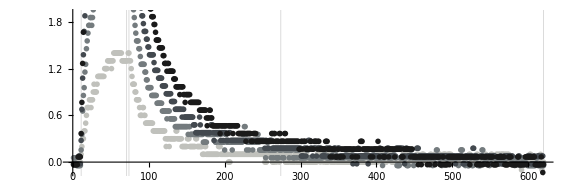

```mathematica
gagTempFitDataPow=ListPlot[gagFitDataPow[[All,1]],
GridLines->{{stimStart,stimEnd,fallStart,fallEnd,trialLength},None}, 
AspectRatio->1/3, ImageSize->72*8,PlotStyle->gagColors]
```

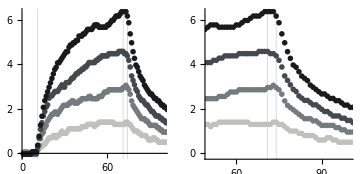

```mathematica
GraphicsRow[
{Show[gagTempFitDataPow,PlotRange->{{0,100},All},AspectRatio->1],
Show[gagTempFitDataPow,PlotRange->{stimStart+stimDuration+{-25,+25},All},AspectRatio->1]}, ImageSize->Medium]
```

## Cleaner Plots

```mathematica
Dimensions[Transpose[{gagFitDataPow,gagColors}]]
```

{4,2}

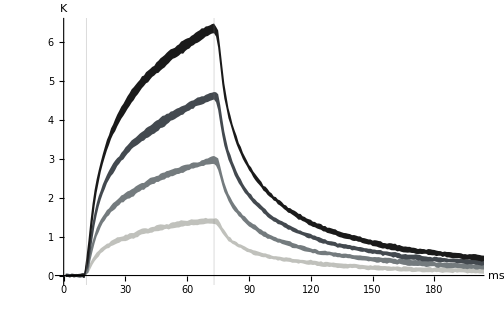

```mathematica
grSDPow=Show[meanBandPlot[#[[1]],#[[2]]]& /@ Transpose[{gagFitDataPow,gagColors}],
GridLines->{{stimStart,stimEnd+2},None}, PlotRange->{{0,200},All},AspectRatio->1/GoldenRatio,ImageSize->72*7, AxesLabel->{"ms", "K"},Ticks->{Automatic,Automatic}, 
AxesStyle->Thickness[0.0025], BaseStyle->{FontFamily->"Helvetica"},AxesOrigin->{0,0}]
```

```mathematica
legend={"2.5","5","7.5","20"};
```

```mathematica
gagLegend=SwatchLegend[gagColors,legend,LabelStyle->{FontSize->10,FontWeight->"Bold"},LegendMargins->5,LegendLayout->"Row",LegendLabel->"Power [mW]"]
```

```mathematica
(*gagLegend=BarLegend[{gagColors,{0,200}},LegendMarkers-> {{20,40}},LabelStyle->{FontSize->10,FontWeight->"Bold"},LegendMargins->5,LegendLayout->"Row",LegendLabel->"Lapsed Time [mins]"]*)
```

```mathematica
gagLegend=Graphics[
Table[
{gagColors[[n+1]],EdgeForm[Directive[Thin,Black]],Rectangle[{-10+n*20, 0},{10+n*20, 5}], Black, Text[legend[[n+1]],{n*20, 0},{0,1.5},BaseStyle->{FontSize->9,Bold}]}, 
{n,0,3}], PlotLabel->Style["Power [mW]",FontWeight->Bold,FontColor->Black,FontSize->9], AspectRatio->1/10,ImageSize->72*1.5
]
```

-Graphics-

```mathematica
(*gagLegend=BarLegend[{gagColors,{-10,210}},10,LabelStyle->{FontSize->10,FontWeight->"Bold"},LegendMargins->5,LegendLayout->"Row",LegendLabel->"Lapsed Time [mins]"]*)
```

```mathematica
(*gagLegend2= SwatchLegend[{Opacity[0.15,Blue]}, {"Laser Stimulation"},LabelStyle->{FontSize->10,FontWeight->"Bold"},LegendMargins->{{53,54},{5,5}},LegendLayout->"Row",LegendFunction->(Framed[#]&)]*)
```

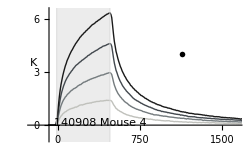

```mathematica
grSDPow=Show[
Show[meanPlot[#[[1]],#[[2]],{-11,620-11}*samplingRate]& /@ Transpose[{gagFitDataPow,gagColors}],ImageSize->72*3.5,
GridLines->{{stimStart-12,stimEnd-11+1}*samplingRate,None},GridLinesStyle->Thickness[0.0025],PlotRange->{{-30,210}*samplingRate,{-0.8,6.5}},AspectRatio->1/GoldenRatio, AxesLabel->{None, None},Ticks->{Table[n,{n,0,1500,250}],{0,1,2,3,4,5,6}},TicksStyle->Directive[Black,9],
AxesStyle->Thickness[0.004], BaseStyle->{FontFamily->"Helvetica"},AxesOrigin->{-10*samplingRate,0},LabelStyle->{FontSize->9,FontWeight->"Bold"},
(*PlotLabel->  "Average temperature increase through time",*)
Prolog->{Opacity[0.15,Gray], Rectangle[{(stimStart-12)*samplingRate,-1},{(stimEnd-11+1)*samplingRate,7}]},
Epilog->{Text["ms",{101*samplingRate,-1},BaseStyle->{FontSize->9,FontWeight->"Bold"}],Text["K",{-28*samplingRate,3.5},BaseStyle->{FontSize->9,FontWeight->"Bold"}],
Inset[gagLegend,{145*samplingRate,4}],Text["140908 Mouse 4",{50*samplingRate,0.12},BaseStyle->{FontSize->2}]}]
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140908 Mouse 4(Power correlation)

```mathematica
Export["140908.AveragePowCorr.png",grSDPow,ImageResolution->600]
```

140908.AveragePowCorr.png

```mathematica
Export["140908.AveragePowCorr.pdf",grSDPow,ImageResolution->600]
```

140908.AveragePowCorr.pdf

```mathematica
gagMeanDataPow= Mean/@gagFitDataPow;
```

```mathematica
Dimensions[gagMeanDataPow]
```

{4,620}

```mathematica
gagMaxDataPow=Max/@gagMeanDataPow
```

{1.40731,2.97135,4.62251,6.35409}

```mathematica
gagMaxDataPow=Map[ToString[NumberForm[#,{3,2}],OutputForm]&,gagMaxDataPow,{1}]
```

{1.41,2.97,4.62,6.35}

```mathematica
gagMaxDataPow=ToExpression[gagMaxDataPow]
```

{1.41,2.97,4.62,6.35}

```mathematica
Options[BarChart]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BarOrigin→Bottom,BarSpacing→Automatic,BaselinePosition→Automatic,BaseStyle→{},ChartBaseStyle→Automatic,ChartElementFunction→Automatic,ChartElements→Automatic,ChartLabels→None,ChartLayout→Automatic,ChartLegends→None,ChartStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,Joined→False,LabelingFunction→Automatic,LabelStyle→{},LegendAppearance→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

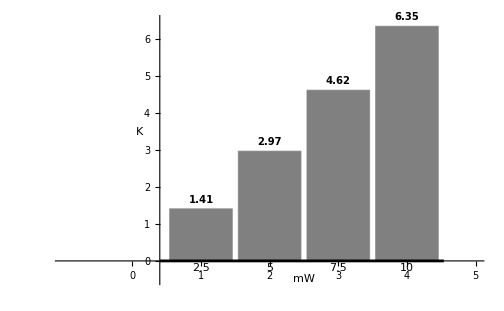

```mathematica
gagMaxTempGraph=BarChart[gagMaxDataPow,
PlotRange->{{-1,5},{-0.5,6.5}},
ChartLabels->{{"2.5","5","7.5","10"}},
AspectRatio->1/GoldenRatio,ImageSize->72*7,AxesStyle->{Directive[Black,Thickness[0.004],FontSize->12],Directive[Black,Thickness[0.004],FontSize->12]}, ChartBaseStyle->{FontFamily->"Helvetica",FontSize->12,FontWeight->Bold},AxesOrigin->{0.4,0},
Ticks->{{0,1,2,3,4,5,6}},ChartStyle->Gray,TicksStyle->Bold,
LabelingFunction->Above,LabelStyle->{FontWeight->Bold,FontSize->10},
Epilog->{Text["mW",{2.5,-0.5},BaseStyle->{FontSize->12,FontWeight->"Bold"}],Text["K",{0.1,3.5},BaseStyle->{FontSize->12,FontWeight->"Bold"}]}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140908 Mouse 4(Power correlation)

```mathematica
Export["140908.PowMaxTemp.png",gagMaxTempGraph]
```

140908.PowMaxTemp.png

```mathematica
Export["140908.PowMaxTemp.pdf",gagMaxTempGraph]
```

140908.PowMaxTemp.pdf

## Change data to {{time,value}, ....} format and Fit Functions

```mathematica
gagMakeTrialXY[data_, startPoint_Integer, endPoint_Integer]:=Module[{gagTimecourseR},
gagTimecourseR =Range[0, endPoint-startPoint ] *samplingRate;
Flatten[ 
Transpose[{gagTimecourseR,#[[startPoint;;endPoint]]}]&  /@ data,   1
]
];
```

```mathematica
gagModelModelRLog[data_, startPoint_Integer, endPoint_Integer]:=
Module[{tempFunc, tempShift},
Simplify[Evaluate[
NonlinearModelFit[gagMakeTrialXY[data,startPoint, endPoint],  
{0.4*a*Log[0.01*c* x+0.1*b]},
{a,b,c},x]]] 
];
```

```mathematica
gagModelShiftFactorRLog[data_, startPoint_Integer, endPoint_Integer]:=
Module[{tempFunc,tempShift},
tempFunc=gagModelFuncRLog[data, startPoint, endPoint];
tempShift= x /. Flatten[Solve[ Evaluate[tempFunc[x]]==0, x]];
tempShift
];
```

```mathematica
gagModelFuncRLog[data_, startPoint_Integer, endPoint_Integer]:=
Module[{tempFunc},
tempFunc=gagModelModelRLog[data, startPoint, endPoint]["BestFit"];
Evaluate[tempFunc /. x->#]&
];
```

```mathematica
gagModelModelFExp[data_, startPoint_Integer, endPoint_Integer]:=
Module[{},
Simplify[Evaluate[
NonlinearModelFit[gagMakeTrialXY[data,startPoint, endPoint],  
{a*ⅇ^(b*(x+7)) +aa*ⅇ^(b*bb*(x+90)),{0 < a<5,-0.5<b<-0.0001 ,0<aa<5,0<bb<1}},
{a,c,b,aa,bb,cc},x]]]
];
```

```mathematica
gagModelFuncFExp[data_, startPoint_Integer, endPoint_Integer]:=
Module[{tempFunc},
tempFunc=gagModelModelFExp[data, startPoint, endPoint]["BestFit"] ;
Evaluate[tempFunc /. x->#]&
];
```

```mathematica
Manipulate[
Show[grSDPow,Plot[a*ⅇ^(b*(x)) +aa*ⅇ^(bb*(x)),{x,fallStart,trialLength},PlotRange->All],
PlotRange->All],
{{a,230.},0,1500},{{b,-0.0612},-0.2,0.2},{{aa,0.31},0,5},{{bb,0.0075},-1,0.3}
];
```

## Fit Function BootStrap

```mathematica
gagBootStrapData=Table[RandomSample[#,10],{500}]& /@gagFitDataPow;
Dimensions[gagBootStrapData]
```

{4,500,10,620}

```mathematica
gagBootStrapModel= ParallelMap[gagModelModelRLog[#,stimStart, stimEnd]&, gagBootStrapData[[#]]]& /@Range[4];
Dimensions[gagBootStrapModel]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{4,500}

```mathematica
gagBootStrapModelParams=#["BestFitParameters"]&/@gagBootStrapModel[[#]]&/@Table[x,{x,1,4,1}];
Dimensions[gagBootStrapModelParams]
```

{4,500,3}

```mathematica
gagBootStrapModelParams=Transpose[gagBootStrapModelParams,{1,3,2}];
Dimensions[gagBootStrapModelParams]
```

{4,3,500}

```mathematica
gagBootStrapModelParams={a/.#& /@gagBootStrapModelParams[[;;,1,#]]*0.4&/@Table[x,{x,1,500,1}],b/.#& /@gagBootStrapModelParams[[;;,2,#]]*0.1&/@Table[x,{x,1,500,1}],c/.#& /@gagBootStrapModelParams[[;;,3,#]]*0.01&/@Table[x,{x,1,500,1}]};
Dimensions[gagBootStrapModelParams]
```

{3,500,4}

```mathematica
gagBootStrapModelParams=Transpose[gagBootStrapModelParams,{1,3,2}];
Dimensions[gagBootStrapModelParams]
```

{3,4,500}

```mathematica
gagBootStrapModelParams=Transpose[gagBootStrapModelParams,{2,1,3}];
Dimensions[gagBootStrapModelParams]
```

{4,3,500}

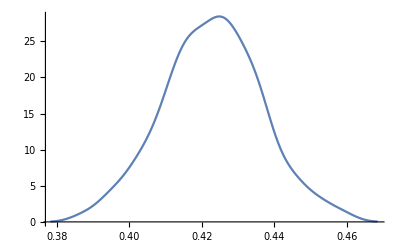
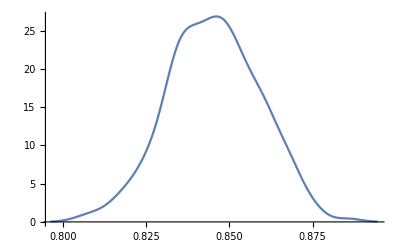
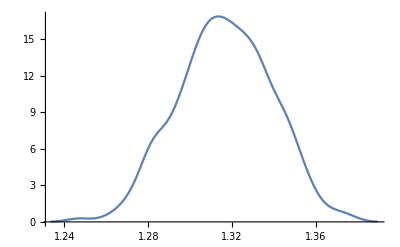
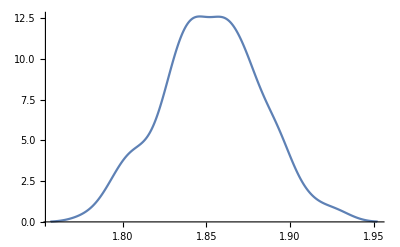
5
6[{{-Graphics-,0.991066},{-Graphics-,0.730232},{-Graphics-,0.762676},{-Graphics-,0.949916}}]

```mathematica
{SmoothHistogram[gagBootStrapModelParams[[#,1]]],DistributionFitTest[gagBootStrapModelParams[[#,1]]]}&/@Table[x,{x,1,4,1}]//TableForm[{5,6}]
```

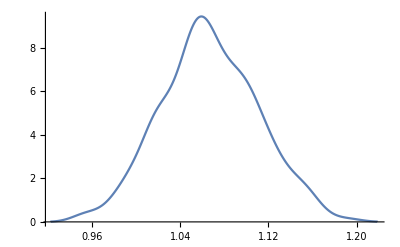
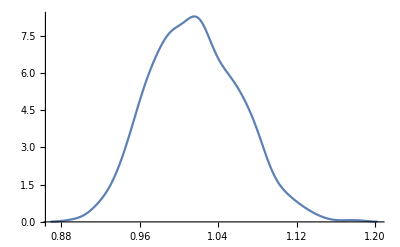
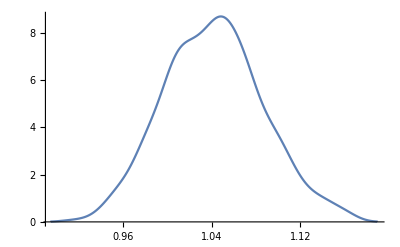
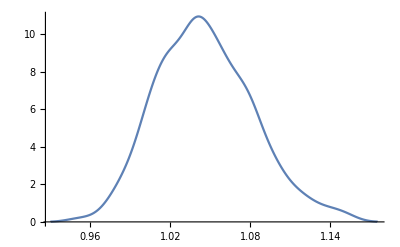
5
6[{{-Graphics-,0.991066},{-Graphics-,0.730232},{-Graphics-,0.762676},{-Graphics-,0.949916}}]

```mathematica
{SmoothHistogram[gagBootStrapModelParams[[#,2]]],DistributionFitTest[gagBootStrapModelParams[[#,1]]]}&/@Table[x,{x,1,4,1}]//TableForm[{5,6}]
```

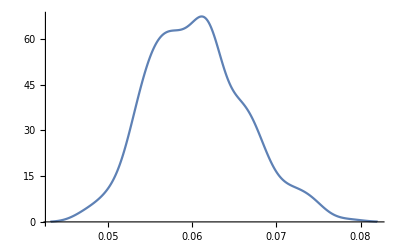
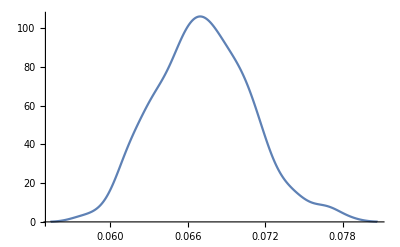
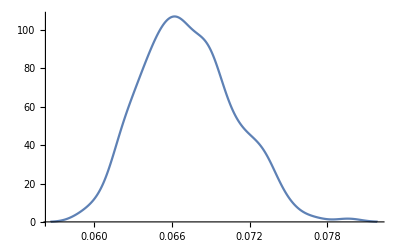
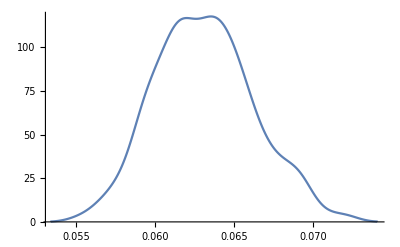
5
6[{{-Graphics-,0.991066},{-Graphics-,0.730232},{-Graphics-,0.762676},{-Graphics-,0.949916}}]

```mathematica
{SmoothHistogram[gagBootStrapModelParams[[#,3]]],DistributionFitTest[gagBootStrapModelParams[[#,1]]]}&/@Table[x,{x,1,4,1}]//TableForm[{5,6}]
```

```mathematica
gagBootStrapModelParamsMedian=Transpose[Median[#]&/@gagBootStrapModelParams[[#]]&/@Range[4]];
Dimensions[gagBootStrapModelParamsMedian]
```

{3,4}

```mathematica
gagBootStrapModelParams99= Transpose[Quantile[#,{0.01,0.99},{{1/2,0},{0,1}}]&/@gagBootStrapModelParams[[#]]&/@Range[4],{2,1,3}];
Dimensions[gagBootStrapModelParams99]
```

{3,4,2}

```mathematica
gagBootStrapModelParamsMedian0=gagBootStrapModelParamsMedian;
```

```mathematica
gagBootStrapModelParamsMedian0={Range[4],#}&/@gagBootStrapModelParamsMedian0;
Dimensions[gagBootStrapModelParamsMedian0]
```

{3,2,4}

```mathematica
gagBootStrapModelParamsMedian0=Transpose[gagBootStrapModelParamsMedian0,{1,3,2}];
```

```mathematica
Needs["ErrorBarPlots`"]
```

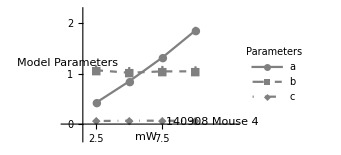

```mathematica
gagAvalueBootStrapGraph=ErrorListPlot[
Transpose[{gagBootStrapModelParamsMedian0,
Map[ErrorBar,
(gagBootStrapModelParams99-gagBootStrapModelParamsMedian0[[;;,;;,2]]),
{2}
]
},{3,1,2}],

Joined->True,ImageSize->72*3.5,
PlotRange->{{0.05,5.2},{-0.3,2.25}},AspectRatio->1/GoldenRatio,AxesStyle->Thickness[0.004], BaseStyle->{FontFamily->"Helvetica"},AxesOrigin->{0.6,0},LabelStyle->{FontSize->9,FontWeight->"Bold"},
PlotMarkers->{Automatic,Medium},
PlotLegends-> Placed[LineLegend[{"a","b","c"},LegendMarkers->{Automatic},LabelStyle->9,LegendMarkerSize->{20,10},LegendLabel->Style["Parameters",FontWeight->Bold,FontSize->9]],{{0.95,0.52},{0.7,0.5}}],
PlotStyle->{Gray,Directive[Gray,Dashed],Directive[Gray,DotDashed]},Ticks->{{{1,"2.5"},{2,"5"},{3,"7.5"},{4,"10"}},{0,0.5,1,1.5,2}},TicksStyle->Directive[Black,9],Epilog->{Text["mW",{2.5,-0.25},BaseStyle->{FontSize->9,FontWeight->"Bold"}],Rotate[Text["Model Parameters",{0.15,1.2},BaseStyle->{FontSize->9,FontWeight->"Bold"}],90 Degree],Text["140908 Mouse 4",{4.5,0.05},BaseStyle->{FontSize->2}]}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140908 Mouse 4(Power correlation)

```mathematica
Export["140908.A-valueBootstrap.png",gagAvalueBootStrapGraph,ImageResolution->600]
```

140908.A-valueBootstrap.png

```mathematica
Export["140908.A-valueBootstrap.pdf",gagAvalueBootStrapGraph,ImageResolution->600]
```

140908.A-valueBootstrap.pdf

```mathematica
gagBootStrapModelParamsMedian0
```

{{{1,0.423047},{2,0.845334},{3,1.31658},{4,1.8529}},{{1,1.06478},{2,1.01539},{3,1.04227},{4,1.0433}},{{1,0.0603374},{2,0.0671406},{3,0.0668736},{4,0.0630442}}}

```mathematica
gagBootStrapModelParamsMedian1=Transpose[Median[#]&/@gagBootStrapModelParams[[#]]&/@Range[4]]
```

{{0.423047,0.845334,1.31658,1.8529},{1.06478,1.01539,1.04227,1.0433},{0.0603374,0.0671406,0.0668736,0.0630442}}

```mathematica
gagBootStrapModelParamsMedian1=ToString[NumberForm[#,{3,2}]]&/@gagBootStrapModelParamsMedian1
```

{{0.42, 0.85, 1.32, 1.85},{1.06, 1.02, 1.04, 1.04},{0.06, 0.07, 0.07, 0.06}}

```mathematica
gagBootStrapModelParamsMedian1=ToExpression[gagBootStrapModelParamsMedian1]
```

{{0.42,0.85,1.32,1.85},{1.06,1.02,1.04,1.04},{0.06,0.07,0.07,0.06}}

```mathematica
gagBootStrapModelParams991=ToString[NumberForm[#,{3,2}]]&/@gagBootStrapModelParams99
```

{{{0.39, 0.46}, {0.81, 0.88}, {1.27, 1.37}, {1.79, 1.92}},{{0.96, 1.16}, {0.92, 1.13}, {0.95, 1.15}, {0.98, 1.14}},{{0.05, 0.07}, {0.06, 0.08}, {0.06, 0.08}, {0.06, 0.07}}}

```mathematica
gagBootStrapModelParams991=ToExpression[gagBootStrapModelParams991]
```

{{{0.39,0.46},{0.81,0.88},{1.27,1.37},{1.79,1.92}},{{0.96,1.16},{0.92,1.13},{0.95,1.15},{0.98,1.14}},{{0.05,0.07},{0.06,0.08},{0.06,0.08},{0.06,0.07}}}

```mathematica
gagBootStrapModelParams991=gagBootStrapModelParams991-gagBootStrapModelParamsMedian1
```

{{{-0.03,0.04},{-0.04,0.03},{-0.05,0.05},{-0.06,0.07}},{{-0.1,0.1},{-0.1,0.11},{-0.09,0.11},{-0.06,0.1}},{{-0.01,0.01},{-0.01,0.01},{-0.01,0.01},{0.,0.01}}}

```mathematica
gagCValueBootStrapData=Table[gagBootStrapModelParamsMedian1[[i,j]]->gagBootStrapModelParams991[[i,j]],{i,1,Length[gagBootStrapModelParamsMedian1]},{j,1,Length[gagBootStrapModelParamsMedian1[[1]]]}]
```

{{0.42→{-0.03,0.04},0.85→{-0.04,0.03},1.32→{-0.05,0.05},1.85→{-0.06,0.07}},{1.06→{-0.1,0.1},1.02→{-0.1,0.11},1.04→{-0.09,0.11},1.04→{-0.06,0.1}},{0.06→{-0.01,0.01},0.07→{-0.01,0.01},0.07→{-0.01,0.01},0.06→{0.,0.01}}}

```mathematica
errorBar[type_:"Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{errorN,errorP},{errorN=Flatten[meta],errorP=Flatten[meta]};
{errorN,errorP}=If[{errorN,errorP}==={},0,Last[{errorN,errorP}]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Thickness[0.0055],Line[{{{(x0+x1)/2,y1+errorN},{(x0+x1)/2,y1+errorP}},{{1/4 (3 x0+x1),y1+errorP},{1/4 (x0+3 x1),y1+errorP}},{{1/4 (3 x0+x1),y1+errorN},{1/4 (x0+3 x1),y1+errorN}}}]}}]
```

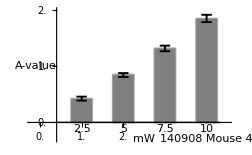

```mathematica
gagCValueBootStrapGraph=BarChart[gagCValueBootStrapData[[1]],ChartElementFunction->errorBar["Rectangle"],ImageSize->72*3.5,
PlotRange->{{-0.2,4.5},{-0.3,2}},
ChartLabels->{{"2.5","5","7.5","10"}},LabelStyle->{FontSize->9,FontWeight->"Bold"},BarSpacing->1,ChartBaseStyle->EdgeForm[Thickness[0.00595]],
AspectRatio->1/GoldenRatio,AxesStyle->{Directive[Black,Thickness[0.004],FontSize->9],Directive[Black,Thickness[0.004],FontSize->9]}, ChartBaseStyle->{FontFamily->"Helvetica",FontSize->9,FontWeight->Bold},AxesOrigin->{0.4,0},
Ticks->{Table[n,{n,0,2,0.5}]},TicksStyle->Directive[Black,9],ChartStyle->Gray,TicksStyle->Bold,LabelStyle->{FontWeight->Bold,FontSize->9},
Epilog->{Text["mW",{2.5,-0.3},BaseStyle->{FontSize->9,FontWeight->"Bold"}],Rotate[Text["A-value",{-0.1,1},BaseStyle->{FontSize->9,FontWeight->"Bold"}],90 Degree],Text["140908 Mouse 4",{4,-0.3},BaseStyle->{FontSize->2}]}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140908 Mouse 4(Power correlation)

```mathematica
Export["140908.PowerCorrA-ValuegagCValueBootStrap.png",gagCValueBootStrapGraph,ImageResolution->600]
```

140908.PowerCorrA-ValuegagCValueBootStrap.png

```mathematica
Export["140908.PowerCorrA-ValuegagCValueBootStrap.pdf",gagCValueBootStrapGraph,ImageResolution->600]
```

140908.PowerCorrA-ValuegagCValueBootStrap.pdf

```mathematica
gagBootStrapModelParamsMedian={gagBootStrapModelParamsMedian,gagBootStrapModelParams99};
```

```mathematica
Dimensions[gagBootStrapModelParamsMedian]
```

{2,3,4}

```mathematica
gagBootStrapModelParamsMedian=Transpose[gagBootStrapModelParamsMedian,{3,1,2}]
Dimensions[gagBootStrapModelParamsMedian]
```

{{{0.423047,{0.391372,0.456128}},{0.845334,{0.811337,0.875696}},{1.31658,{1.26705,1.36837}},{1.8529,{1.78802,1.92464}}},{{1.06478,{0.961906,1.16382}},{1.01539,{0.920268,1.12819}},{1.04227,{0.946392,1.15056}},{1.0433,{0.975239,1.14325}}},{{0.0603374,{0.048316,0.0745688}},{0.0671406,{0.0594454,0.0768994}},{0.0668736,{0.0600496,0.0757173}},{0.0630442,{0.0565133,0.0706376}}}}

{3,4,2}

```mathematica
gagBootStrapModelParamsMedian=Map[(ToString[NumberForm[#[[1]],{3,2}]] <> " ("<>ToString[NumberForm[#[[2,1]],{3,2}]]<>"-"<>ToString[NumberForm[#[[2,2]],{3,2}]]<>")" )&, gagBootStrapModelParamsMedian,{2}]
```

{{0.42 (0.39-0.46),0.85 (0.81-0.88),1.32 (1.27-1.37),1.85 (1.79-1.92)},{1.06 (0.96-1.16),1.02 (0.92-1.13),1.04 (0.95-1.15),1.04 (0.98-1.14)},{0.06 (0.05-0.07),0.07 (0.06-0.08),0.07 (0.06-0.08),0.06 (0.06-0.07)}}

```mathematica
gagBootStrapModelParamsMedian=Prepend[gagBootStrapModelParamsMedian,{"Power [mw]",2.5,5,7.5,10}];
Dimensions[gagBootStrapModelParamsMedian]
```

{4}

```mathematica
gagBootStrapModelParamsMedian[[2]]
```

{0.42 (0.39-0.46),0.85 (0.81-0.88),1.32 (1.27-1.37),1.85 (1.79-1.92)}

```mathematica
gagBootStrapModelParamsMedian[[2]]= Prepend[gagBootStrapModelParamsMedian[[2]],"a (1%CI-99%CI)"];
```

```mathematica
gagBootStrapModelParamsMedian[[3]]= Prepend[gagBootStrapModelParamsMedian[[3]],"b (1%CI-99%CI)"];
```

```mathematica
gagBootStrapModelParamsMedian[[4]]= Prepend[gagBootStrapModelParamsMedian[[4]],"c (1%CI-99%CI)"];
```

```mathematica
Options[Grid]
```

{Alignment→{Center,Baseline},AllowedDimensions→Automatic,AllowScriptLevelChange→True,AutoDelete→False,Background→None,BaselinePosition→Automatic,BaseStyle→{},DefaultBaseStyle→Grid,DefaultElement→□,DeleteWithContents→True,Dividers→{},Editable→Automatic,Frame→None,FrameStyle→Automatic,ItemSize→Automatic,ItemStyle→None,Selectable→Automatic,Spacings→Automatic}

```mathematica
gagBootStrapModelParamsMedian//InputForm
```

{{"Power [mw]", 2.5, 5, 7.5, 10}, {"a (1%CI-99%CI)", "0.42 (0.39-0.46)", "0.85 (0.81-0.88)", "1.32 (1.27-1.37)", "1.85 (1.79-1.92)"}, 
 {"b (1%CI-99%CI)", "1.06 (0.96-1.16)", "1.02 (0.92-1.13)", "1.04 (0.95-1.15)", "1.04 (0.98-1.14)"}, {"c (1%CI-99%CI)", "0.06 (0.05-0.07)", "0.07 (0.06-0.08)", "0.07 (0.06-0.08)", "0.06 (0.06-0.07)"}}

```mathematica
gagParamsTableBootStrap=Grid[gagBootStrapModelParamsMedian,Frame->All,ItemSize->{{1->9,2;;12->8},1.5},BaseStyle->{FontSize->9,FontFamily->"Helvetica"},ItemStyle->{{Bold},{Directive[Bold,FontFamily->"Helvetica"],FontFamily->"Helvetica",FontFamily->"Helvetica",FontFamily->"Helvetica"}},Dividers->{{2->Thick},{2->Thick}},Background->{None,{2->Opacity[0.35,Gray]}}(*,BaseStyle{FontFamily->"Helvetica"}*)]
```

Power [mw] | 2.5 | 5 | 7.5 | 10
a (1%CI-99%CI) | 0.42 (0.39-0.46) | 0.85 (0.81-0.88) | 1.32 (1.27-1.37) | 1.85 (1.79-1.92)
b (1%CI-99%CI) | 1.06 (0.96-1.16) | 1.02 (0.92-1.13) | 1.04 (0.95-1.15) | 1.04 (0.98-1.14)
c (1%CI-99%CI) | 0.06 (0.05-0.07) | 0.07 (0.06-0.08) | 0.07 (0.06-0.08) | 0.06 (0.06-0.07)

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140908 Mouse 4(Power correlation)

```mathematica
Export["140908.ParamsTableBootStrap.png",gagParamsTableBootStrap,ImageResolution->600]
```

140908.ParamsTableBootStrap.png

```mathematica
Export["140908.ParamsTableBootStrap.pdf",gagParamsTableBootStrap,ImageResolution->600]
```

140908.ParamsTableBootStrap.pdf

## Fit Function

```mathematica
{funcR1,funcR2, funcR3, funcR4}=gagModelFuncRLog[#,stimStart, stimEnd]& /@gagFitDataPow
```

{0.423221 Log[1.06722+0.0600435 #1]&,0.844654 Log[1.01653+0.0671969 #1]&,1.31688 Log[1.03661+0.0669772 #1]&,1.85304 Log[1.04473+0.0629295 #1]&}

```mathematica
{modelR1,modelR2, modelR3, modelR4}=gagModelModelRLog[#,stimStart, stimEnd]& /@gagFitDataPow;
```

```mathematica
gagModelParams={modelR1["BestFitParameters"],modelR2["BestFitParameters"],modelR3["BestFitParameters"],modelR4["BestFitParameters"]};
```

```mathematica
gagModelParams=Transpose[gagModelParams]
```

{{a→1.05805,a→2.11164,a→3.2922,a→4.63259},{b→10.6722,b→10.1653,b→10.3661,b→10.4473},{c→6.00435,c→6.71969,c→6.69772,c→6.29295}}

```mathematica
gagModelParams={a/.#& /@gagModelParams[[1]]*0.4,b/.#& /@gagModelParams[[2]]*0.1,c/.#& /@gagModelParams[[3]]*0.01}
```

{{0.423221,0.844654,1.31688,1.85304},{1.06722,1.01653,1.03661,1.04473},{0.0600435,0.0671969,0.0669772,0.0629295}}

```mathematica
gagModelParams0=gagModelParams
```

{{0.423221,0.844654,1.31688,1.85304},{1.06722,1.01653,1.03661,1.04473},{0.0600435,0.0671969,0.0669772,0.0629295}}

```mathematica
gagModelParams=Map[ToString[NumberForm[#,{4,3}]]&,gagModelParams,{2}]
```

{{0.423,0.845,1.317,1.853},{1.067,1.017,1.037,1.045},{0.060,0.067,0.067,0.063}}

```mathematica
gagModelParams1=ToExpression[gagModelParams]
```

{{0.423,0.845,1.317,1.853},{1.067,1.017,1.037,1.045},{0.06,0.067,0.067,0.063}}

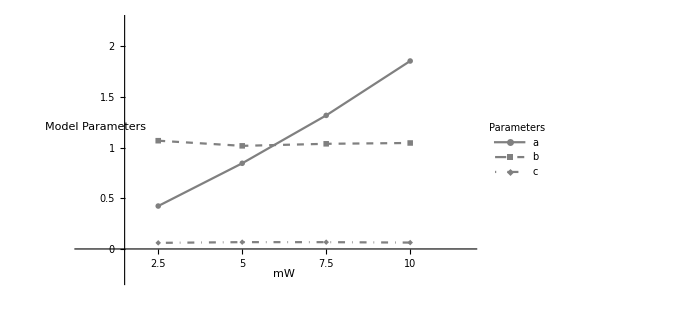

```mathematica
gagAvalueGraph=ListLinePlot[
gagModelParams0, 
PlotRange->{{0.1,4.7},{-0.3,2.25}},AspectRatio->1/GoldenRatio,ImageSize->72*7,AxesStyle->Thickness[0.004], BaseStyle->{FontFamily->"Helvetica"},AxesOrigin->{0.6,0},LabelStyle->{FontSize->12,FontWeight->"Bold"},
PlotMarkers->{Automatic,Medium},
PlotLegends-> Placed[LineLegend[{"a","b","c"},LegendMarkers->{Automatic},LegendLabel->Style["Parameters",FontWeight->Bold]],{{0.95,0.32},{0.7,0.5}}],
PlotStyle->{Gray,Directive[Gray,Dashed],Directive[Gray,DotDashed]},Ticks->{{{1,"2.5"},{2,"5"},{3,"7.5"},{4,"10"}},{0,0.5,1,1.5,2}},Epilog->{Text["mW",{2.5,-0.25},BaseStyle->{FontSize->12,FontWeight->"Bold"}],Rotate[Text["Model Parameters",{0.25,1.2},BaseStyle->{FontSize->12,FontWeight->"Bold"}],90 Degree]}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140908 Mouse 4(Power correlation)

```mathematica
Export["140908.A-value.png",gagAvalueGraph]
```

140908.A-value.png

```mathematica
Export["140908.A-value.pdf",gagAvalueGraph]
```

140908.A-value.pdf

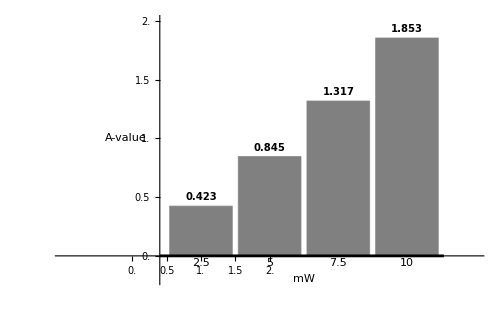

```mathematica
gagCValueGraph=BarChart[gagModelParams1[[1]],
PlotRange->{{-1,5},{-0.2,2}},
ChartLabels->{{"2.5","5","7.5","10"}},
AspectRatio->1/GoldenRatio,ImageSize->72*7,AxesStyle->{Directive[Black,Thickness[0.004],FontSize->12],Directive[Black,Thickness[0.004],FontSize->12]}, ChartBaseStyle->{FontFamily->"Helvetica",FontSize->12,FontWeight->Bold},AxesOrigin->{0.4,0},
Ticks->{Table[n,{n,0,2,0.5}]},ChartStyle->Gray,TicksStyle->Bold,
LabelingFunction->Above,LabelStyle->{FontWeight->Bold,FontSize->10},
Epilog->{Text["mW",{2.5,-0.2},BaseStyle->{FontSize->12,FontWeight->"Bold"}],Rotate[Text["A-value",{-0.1,1},BaseStyle->{FontSize->12,FontWeight->"Bold"}],90 Degree]}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140908 Mouse 4(Power correlation)

```mathematica
Export["140908.PowerCorrA-Value.png",gagCValueGraph]
```

140908.PowerCorrA-Value.png

```mathematica
Export["140908.PowerCorrA-Value.pdf",gagCValueGraph]
```

140908.PowerCorrA-Value.pdf

```mathematica
gagModelParams=Prepend[gagModelParams,{"Power [mw]",2.5,5,7.5,10}];
```

```mathematica
gagModelParams[[4]]
```

{0.060,0.067,0.067,0.063}

```mathematica
gagModelParams[[2]]= Prepend[gagModelParams[[2]],"a"];
```

```mathematica
gagModelParams[[3]]= Prepend[gagModelParams[[3]],"b"];
```

```mathematica
gagModelParams[[4]]= Prepend[gagModelParams[[4]],"c"];
```

```mathematica
gagModelParams//InputForm
```

{{"Power [mw]", 2.5, 5, 7.5, 10}, {"a", "0.423", "0.845", "1.317", "1.853"}, 
 {"b", "1.067", "1.017", "1.037", "1.045"}, {"c", "0.060", "0.067", "0.067", "0.063"}}

```mathematica
gagParamsTable=Grid[gagModelParams,Frame->All,ItemSize->{Automatic,2},ItemStyle->{{Bold},{Directive[Bold,FontFamily->"Helvetica"],FontFamily->"Helvetica",FontFamily->"Helvetica",FontFamily->"Helvetica"}},Dividers->{{2->Thick},{2->Thick}}(*,BaseStyle{FontFamily->"Helvetica"}*)]
```

Power [mw] | 2.5 | 5 | 7.5 | 10
a | 0.423 | 0.845 | 1.317 | 1.853
b | 1.067 | 1.017 | 1.037 | 1.045
c | 0.060 | 0.067 | 0.067 | 0.063

```mathematica
gagParamsTable//InputForm
```

Grid[{{"Power [mw]", 2.5, 5, 7.5, 10}, {"a", "0.423", "0.845", "1.317", "1.853"}, 
  {"b", "1.067", "1.017", "1.037", "1.045"}, {"c", "0.060", "0.067", "0.067", "0.063"}}, Frame -> All, 
 ItemSize -> {Automatic, 2}, ItemStyle -> {{Bold}, {Directive[Bold, FontFamily -> "Helvetica"], 
    FontFamily -> "Helvetica", FontFamily -> "Helvetica", FontFamily -> "Helvetica"}}, 
 Dividers -> {{2 -> Thickness[Large]}, {2 -> Thickness[Large]}}]

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140908 Mouse 4(Power correlation)

```mathematica
Export["140908.ParamsTable.png",gagParamsTable]
```

140908.ParamsTable.png

```mathematica
Export["140908.ParamsTable.pdf",gagParamsTable]
```

140908.ParamsTable.pdf

```mathematica
{shiftR1,shiftR2, shiftR3, shiftR4}=gagModelShiftFactorRLog[#,stimStart, stimEnd]& /@gagFitDataPow
```

{-1.11952,-0.246021,-0.54661,-0.710831}

```mathematica
grRPlot=Plot[{funcR1[x+shiftR1*samplingRate],funcR2[x+shiftR2*samplingRate], funcR3[x+shiftR3*samplingRate], funcR4[x+shiftR4*samplingRate]},{x,0,(stimEnd+2)*samplingRate}, PlotStyle->gagColors,PlotRange->All];
```

```mathematica
{funcF1,funcF2, funcF3, funcF4}=gagModelFuncFExp[#,fallStart, trialLength]& /@gagFitDataPow
```

{1.00307 ⅇ^(-0.00915645 (7+#1))+0.455748 ⅇ^(-0.00115851 (90+#1))&,2.09494 ⅇ^(-0.00999514 (7+#1))+1.04563 ⅇ^(-0.00132595 (90+#1))&,3.32017 ⅇ^(-0.00964046 (7+#1))+1.52905 ⅇ^(-0.00130065 (90+#1))&,4.47772 ⅇ^(-0.0100031 (7+#1))+2.14597 ⅇ^(-0.00133068 (90+#1))&}

```mathematica
grFPlot=Plot[{funcF1[x-(fallStart-stimStart)*samplingRate],funcF2[x-(fallStart-stimStart)*samplingRate], funcF3[x-(fallStart-stimStart)*samplingRate], funcF4[x-(fallStart-stimStart)*samplingRate]},{x,(fallStart-stimStart)*samplingRate,trialLength*samplingRate}, PlotStyle->gagColors,PlotRange->All];
```

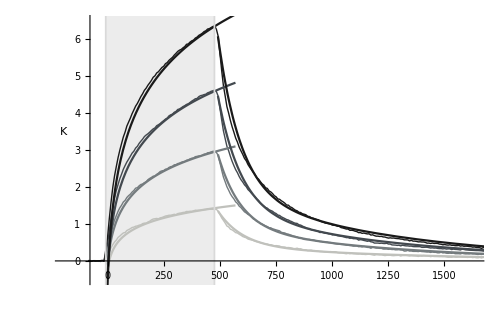

```mathematica
Show[grSDPow,grRPlot,grFPlot]
```